Problema 2

```mathematica
DSolve[{u''[t]-u[t]==0, u[0]==1, u'[0]==-1},u[t],t]
```

{{u[t]→ⅇ^-t}}

```mathematica
DSolve[{u''[t]-u[t]==t Exp[-t], u[0]==0, u'[0]==0},u[t],t]//FullSimplify
```

{{u[t]→1/8 ⅇ^-t (-1+ⅇ^(2 t)-2 t (1+t))}}

```mathematica
DSolve[{u''[t]-u[t]==ϵ t Exp[-t], u[0]==1, u'[0]==-1},u[t],t]//FullSimplify
```

{{u[t]→1/8 ⅇ^-t (8+(-1+ⅇ^(2 t)-2 t (1+t)) ϵ)}}

```mathematica
Series[1/8 ⅇ^-t (8+(-1+ⅇ^(2 t)-2 t (1+t)) ϵ),{t,0,8}]
```

1-t+t^2/2+1/6 (-1+ϵ) t^3+(1/24-ϵ/12) t^4+(-1/120+ϵ/30) t^5+(1/720-ϵ/120) t^6+(-1/5040+ϵ/560) t^7+(1/40320-ϵ/3360) t^8+O[t]^9

#### Computation of sequential higher order derivatives

```mathematica
u2t[t_] = u[t]+ϵ t u[t];
u3t[t_]=D[u2t[t],t] 
u4t[t_]=D[u3t[t],t]
u5t[t_]=D[u4t[t],t]
u6t[t_]=D[u5t[t],t]
u7t[t_]=D[u6t[t],t]
u8t[t_]=D[u7t[t],t]
```

ϵ u[t]+u'[t]+t ϵ u'[t]

2 ϵ u'[t]+u''[t]+t ϵ u''[t]

3 ϵ u''[t]+u^(3)[t]+t ϵ u^(3)[t]

4 ϵ u^(3)[t]+u^(4)[t]+t ϵ u^(4)[t]

5 ϵ u^(4)[t]+u^(5)[t]+t ϵ u^(5)[t]

6 ϵ u^(5)[t]+u^(6)[t]+t ϵ u^(6)[t]

Problema 4

```mathematica
Solve[x^2+2x,x]
```

Solve::naqs: 2 x+x^2 is not a quantified system of equations and inequalities.

```mathematica
Solve[2 x+x^2==0,x]
```

{{x→-2},{x→0}}

```mathematica
Solve[y^3+y^2==0,y]
```

{{y→-1},{y→0},{y→0}}

```mathematica
(a+b)^3//Expand
```

a^3+3 a^2 b+3 a b^2+b^3

Problema 5

Soluciones con del problema no perturbado con BC1 y BC2.

```mathematica
DSolve[{x^(1/3)y'[x]+y[x]==0,y[0]==0},y[x],x]//N//FullSimplify
```

{{y[x]→0.}}

```mathematica
DSolve[{x^(1/3)y'[x]+y[x]==0,y[1]==Exp[-3/2]},y[x],x]//N//FullSimplify
```

{{y[x]→ⅇ^(-1.5 x^(2/3))}}

```mathematica
DSolve[{y''[x]+x^(1/3)y'[x]==0, y[0]==0},y[x],x]//N//FullSimplify
```

{{y[x]→C[1] (1.14038-(0.930605 x Gamma[0.75,0.75 x^(4/3)])/((x^(4/3))^(3/4)))}}

Solución numérica del problema

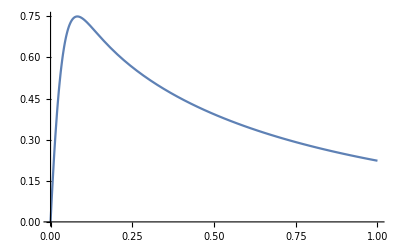

```mathematica
ϵ=0.01;
s =NDSolve[{ϵ y''[x]+x^(1/3)y'[x]+y[x]==0,y[0]==0,y[1]==Exp[-3/2]},y[x],x];
Plot[Evaluate[y[x]/.s],{x,0,1},PlotRange->All]
```

```mathematica
yo[x_]=ⅇ^(-1.5 x^(2/3));
yi[x_]=C[1] (1.140378737738966-(0.9306048591020996 x Gamma[0.75,0.75 x^(4/3)])/((x^(4/3))^(3/4)));
Limit[yi[x],x->0,Direction->-1]
```

0.

```mathematica
(*re-definition of the inner solution*)
```

```mathematica
yi[x_,ϵ_]=C[1] (1.140378737738966-0.9306048591020996 Gamma[0.75,0.75 x^(4/3)/ϵ]);
```

```mathematica
(* trying to find an uniform solution *)
Limit[yo[Sqrt[ϵ]η], ϵ->0, Direction->-1]
Limit[yi[Sqrt[ϵ]η], ϵ->0, Direction->-1]
```

1.

(1.14038-(1.14038 (η^(4/3))^(1/4))/η^(1/3)) C[1]